# Report Project 2 - William Lewin & Elias Chahine wlewin@kth.se, echahine@kth.se

## Summary

### Task

Professor Alice is sending a problem to the student Bob according to the procedure in section Section.Subsection.Subsubsection. You are supposed to solve Bob’s problem. However, you need to start by cracking the cipher sent to Bob. When translating to ASCII, you can assume the base 256.

The numbers is the list seems to be of the same size. Why?
Motivate your selected mathematical model!

Task derived from previous task:

"Congratulations! You have ""now managed to crack the R""SA cipher. Your task is as"" follows: write a method R"SAcrack[cipher,n,e] that w""ill crack a standard RSA c""ipher and delivers clear t""ext from the string cipher"". When you are finished wi"th your method, you should"" investigate how long it w""ill take to crack the ciph""er of the Swedish text DIS"KRET MATTE, DE E FETT NAIS"! for different sizes on y""our public key n (100-200 ""bits). Visualize your resu""lts in a proper graph. It ""is very important that you"" study the section 2.3 in ""the instructions. Your gra""ph should lead you to a mo""del where you can predict ""how long it would take to ""crack a cipher if n is 102""4, 2048 bits or 4096 bits "with your computer.

#### Section.Subsection.Subsubsection Using RSA for Authentication

In RSA it’s not just Alice that can send a message to Bob. Anyone that access Bob’s public keys can sen an encrypted message. So how can Bob know that the message is from Alice?

A rather straight forward way of doing this is that Alice also encrypt the message with her secret key d_Alice. Bob will later decrypt, using Alice’s public key.

Let’s say Alice wants to send a message to Bob.

m_Alice<min(n_Alice,n_Bob)

start with the key that belongs to min(n_Alice,n_Bob)

n_Alice<n_Bob⇒c_0≡_n_Alice m_Alice^d_Alice, c_Alice≡_n_Bob c_0^e_Bob

n_Bob<n_Alice⇒c_0≡_n_Bob m_Alice^e_Bob, c_Alice≡_n_Alice c_0^d_Alice

Bob decrypts the cipher by

start with the key that belongs to max(n_Alice,n_Bob)

n_Bob>n_Alice⇒c_1≡_n_Bob c_Alice^d_Bob, m_Alice≡_n_Alice c_1^e_Alice

n_Alice>n_Bob⇒c_1≡_n_Alice c_Alice^e_Alice, m_Alice≡_n_Bob c_1^d_Bob

Usually the authentication is not done on the full message, but rather a message digest or a cryptographic checksum, e.g. secure hash algorithm (SHA).

### Result

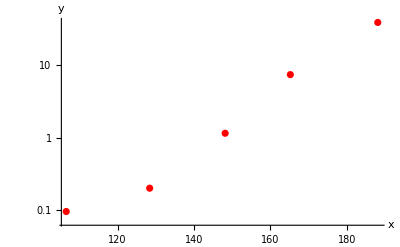
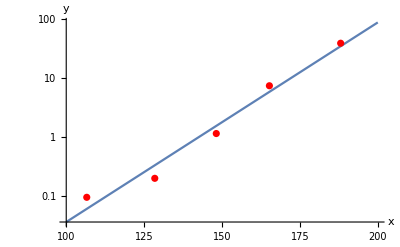
The numbers in the cipher are roughly of the same size because the message needs to be broken down in to smaller pieces (smaller than n) in order for the cracking method to return a unambiguous result. 

After cracking the initial RSA puzzle, we were introduced to a new task. This task involved writing a method for decrypting a cipher and calculating the time required to crack the cipher depending on the size of the size of the public key (N). 
The time required to crack the cipher will strongly depend on the size of N, seeing as the main problem of cracking an RSA cipher is the prime factoring required to reverse the encryption process. 

Approx N. | Processing time
2^(100-110) | 0.087013
2^(120-130) | 0.218892
2^(140-150) | 1.26341
2^(160-170) | 7.85949
2^(180-190) | 41.0367

Our mathematical model of choosing was a power function. As the graph below shows, when plotted as a standard graph, the values show an exponential curve upwards.

Log-graph
-Graphics-
When plotted as a log-log graph, the values are displayed as a straight line. We chose this model based on “If data fits a straight line in a log(y)-log(x) plot, then the model is a power function.”

Log-lin and function graph 
-Graphics-

Based on this model and the data we have gathered, a prediction of the running time of larger N was created. 

N |  Estimated processing time
2^1024 | 8.46925×10^29
2^2048 | 4.97244×10^64
2^4096 | 1.71403×10^134

### Code

#### Part 1 - Alice & Bob

```mathematica
nAlice=14625052655936968690439555839903578410656653152402266773966305647313;
eAlice=9103;
```

```mathematica
nBob=891257371165353198597686733461449215081540410212576138836198818353;
eBob=6389;
```

```mathematica
cipher={4430210573981968733755487447818174029880701596884938356564639003222,2851153559114750987221731555966122250132614620940651980091426872783,7706806242317911603638504323916964668918097951180075641184510131492,3684227409638269668959612918228029487936911649602484180495870360134,118390233898339944208891887229177617429671446231727377499079969939,11722755771961643408261179942790037153532726213028762901063706465880,13859812858423457720552211210177480158021647193707898449643563546715,8458200553283608142592103589289032864817455387331640007234518389001,4203062251335458332458951560795586742826858693125368654700629553235,11246017592897572378455633552556960091533916541949272900160606355164,528729157482321024630053104368111400799635858352035984875544277541,14149609332514930578966644135292557372570883055216115495760639164502,6806693065526086081574819023329054541636484663342321332752294055806,10173212145631688548727430811241580523813551542356631310237779750220,6759760040422316973322423168431166905944837651248859901210533615722,11488644301666039406597033276777701689096765993957684011886918061630,10421162414768710251337302689028405059375889881305351342596162625647,9496359638348947223087997149242581766202717301485526573539185466328,6021527813042783330194131859432644092333420618174656828129608651886,1862712526928231860818857411345402991522792361353775067366437910859,5770870235309404532139302393417410250573907045700501009827409811147,7754796273877044686482387739917927617087893337176831108280229804774,1689445149306311402232833597026076887079752228378923964144759423086,1448530945006829418385610770415140752515002298435493622427431846992,7445869507503892181715468267483205548161014207123217105479157092169,10975830923316626122520530596740793665823967057824410678091427215458,9807539864876132360289770201821020858873102738795986884424480971219};
```

```mathematica
qAlice=3086973200587318781402218709909851;
pAlice=4737667516243564271342073671581763;
pBob = 457792861431456494922119050690577;
qBob = 1946857293446017662241143108141089;
phiBob=(pBob-1)*(qBob-1);
```

```mathematica
c1 = PowerMod[cipher,eAlice,nAlice]
dBob = PowerMod[eBob,-1,phiBob];
```

{444970409279297770090044313053201614952097369301321865917424641258,183674113104017659567913355845229971423316056372265070315906622235,617562464331006011907353184885542978809945586185511937486448993081,692990377295446436150600101814271370870058687365945680092195122174,15829748288796827376895234161254693491217089543931177859749489351,829040669128475076848018289419857381658084508110712186672486418727,798784110186848820585991906620519315059619601235652455703626882470,399074729448818803154154587362403712935004945380245199874499152222,117885647490473600604299228604398634086600112086102442640882667648,558787628279681901598087640588483929735685558225150887948892510920,308098398607398025511582944888788009237158897308762960032967624060,246032490633541021297680837804144220001633329118178930732181456343,553148258011717024187532272757027196386133700023765934740879242061,15757977304317592988100905265851778837698855049986566247100042111,48555750069717983165419507244417369421745602752746641594676113574,645816746709820531252882158812595825630657287083837162388102093670,579143280819432400927730228652650181095648756820602602216165263215,330396900456864364791120284078288409962248134453101589867285929222,30285107152858671427605286391722289914017102065648398433550314482,394905566235612664675691317209814782624147170337593067979209081310,755643239531999740019455828836426484399589590914276018760019795860,271578869017028208773948310614382084613277253285953238316507795669,32235777068746143161753960770773082449807496888435064114936879538,345365485638270886035459127757587129598779123419559816170941440724,491321654189544745328056390015517259287338718673949903009759789721,654607901613345323795924172006966197409745426827819740917539895273,400520866556330100012684699137119966708411863335636746903373549398}

```mathematica
B= 256
For[i=0,i≤  Length[c1], i++,
messageFrom = PowerMod[c1[[i]],dBob,nBob];
q=messageFrom;ascii={};
While[q≠0,
AppendTo[ascii,Mod[q,B]];
q=Quotient[q,B];
]
ascii;
Print[FromCharacterCode[ascii]]]
```

256

Congratulations! You have

now managed to crack the R

SA cipher. Your task is as

follows: write a method R

SAcrack[cipher,n,e] that w

ill crack a standard RSA c

ipher and delivers clear t

ext from the string cipher

. When you are finished wi

th your method, you should

investigate how long it w

ill take to crack the ciph

er of the Swedish text DIS

KRET MATTE, DE E FETT NAIS

! for different sizes on y

our public key n (100-200

bits). Visualize your resu

lts in a proper graph. It

is very important that you

study the section 2.3 in

the instructions. Your gra

ph should lead you to a mo

del where you can predict

how long it would take to

crack a cipher if n is 102

4, 2048 bits or 4096 bits

with your computer.

#### Part 2 - RSAcrack

```mathematica
ClearAll["`*"]
rsaCracker[cipher_,n_,e_]:=Module[{storeAscii,messageFromSomeone,q,ascii,storePrime,pSomebody,qSomebody,phiSomebody
,dSomebody,x,decrypt,storeCrypto},
Array[storePrime,{1,2}];
Array[storeAscii,Length[cipher]];
Array[storeCrypto,Length[cipher]];
storePrime =FactorInteger[n];
pSomebody = First[First[storePrime]];
qSomebody = First[Last[storePrime]];
phiSomebody = (pSomebody-1)*(qSomebody-1);
dSomebody=PowerMod[e,-1,phiSomebody];
For[x=1,x≤ Length[cipher],x++,
decrypt=PowerMod[cipher[[x]],dSomebody,n];
(*Print[FromCharacterCode[Mod[PowerMod[cipher[[x]],dSomebody,n],256]]*)
]
(*Print[FromCharacterCode[PowerMod[cipher[x],dSomebody,n]]];*)
]
```

```mathematica
n1 = 5578181019009693605300014200069239612723;
e1 = 2789;
c1 = {1608192936300849447357116938533648061107,
3368101354959964882647605580669968489491,
2067852446080194085197089058618838874024,
1970950724178345329211485215132189129759,
947134178411813608445435420328616718804,
1925576565744010767772217211256082820941,
4605459822148021013012052952352972584253,
4186841003888572996495111346409155824035,
1846041963789369070974811225481636796431,
5096044390444446125352119889852571089057,
4605459822148021013012052952352972584253,
4605459822148021013012052952352972584253,
1925576565744010767772217211256082820941,
5115617652969099595819651211522229560263,
4186841003888572996495111346409155824035,
1608192936300849447357116938533648061107,
1925576565744010767772217211256082820941,
4186841003888572996495111346409155824035,
1925576565744010767772217211256082820941,
4186841003888572996495111346409155824035,
2041435395349385173865782389645455193305,
1925576565744010767772217211256082820941,
4605459822148021013012052952352972584253,
4605459822148021013012052952352972584253,
4186841003888572996495111346409155824035,
5204069424414112663197882625268745616409,
5096044390444446125352119889852571089057,
3368101354959964882647605580669968489491,
2067852446080194085197089058618838874024,
2986416525605309900776533196503168288929};
t1 = Timing[rsaCracker[c1,n1,e1]]
```

{0.306832,Null}

≈2^100-110

```mathematica
n2 = 121914658243735402103595568170551;
e2 =63619;
c2 = {72223437142745922761712779801658,
33340725534051141497601756886800,
32221412764008165092025682787575,
120681464919026052203103890611480,
59645867002865201046088441793664,
93146411292283398968522997511128,
44754172949140988385706024419890,
48539000215501430549676716832222,
38888168873414911218290508562342,
24945388829311567639254635725552,
44754172949140988385706024419890,
44754172949140988385706024419890,
93146411292283398968522997511128,
25914381598839031224009077432647,
48539000215501430549676716832222,
72223437142745922761712779801658,
93146411292283398968522997511128,
48539000215501430549676716832222,
93146411292283398968522997511128,
48539000215501430549676716832222,
66267839097823468335752547081914,
93146411292283398968522997511128,
44754172949140988385706024419890,
44754172949140988385706024419890,
48539000215501430549676716832222,
66135258968373472547906451453888,
24945388829311567639254635725552,
33340725534051141497601756886800,
32221412764008165092025682787575,
115613677863339485569819355518945};
t2 = Timing[rsaCracker[c2,n2,e2]]
```

{0.094384,Null}

≈2^120-130

```mathematica
n3 = 455655141456960940308510806241646658819;
e3 =77513;
c3 = {229856101785498353633365686324091888062,
6898543326360707900578290633740841130,
155352807959041102282886683051662684796,
314893222850282505783380209933883265562,
70114904766560545494270380740143622926,
179416050484005634773636110729539841447,
259382091522021082769104400203500074135,
86203446659210353812339302068440599223,
247369200372479339628745849133547768022,
231551185461132829182195918270777623595,
259382091522021082769104400203500074135,
259382091522021082769104400203500074135,
179416050484005634773636110729539841447,
142560303329889017622909380182692309072,
86203446659210353812339302068440599223,
229856101785498353633365686324091888062,
179416050484005634773636110729539841447,
86203446659210353812339302068440599223,
179416050484005634773636110729539841447,
86203446659210353812339302068440599223,
185874809763790862698014047508581899317,
179416050484005634773636110729539841447,
259382091522021082769104400203500074135,
259382091522021082769104400203500074135,
86203446659210353812339302068440599223,
170245136740506555122701271711162938767,
231551185461132829182195918270777623595,
6898543326360707900578290633740841130,
155352807959041102282886683051662684796,
310110795247312160025167303315805902060};
t3 = Timing[rsaCracker[c3,n3,e3]]
```

{0.198565,Null}

≈2^140-150

```mathematica
n4 = 399631185399565082910863599325056141232359753;
e4 =38131;
c4 = {178403006527178050571555949039536217650435227,
382333861151321333498960151740199072902842743,
1761584675590839734287976390632540296552968,
22404752690349690053084894825719736337297688,
165821407921528136252805764703861101446997623,
240364220141028992626632272034750921311523065,
302590304340353376349353538444305692106774979,
101560557675965682301030257770383367178916685,
62888716702837907792667650514263321420354985,
128032200604782244713434477043518271901000964,
302590304340353376349353538444305692106774979,
302590304340353376349353538444305692106774979,
240364220141028992626632272034750921311523065,
367975550705439116208504452788241548070322850,
101560557675965682301030257770383367178916685,
178403006527178050571555949039536217650435227,
240364220141028992626632272034750921311523065,
101560557675965682301030257770383367178916685,
240364220141028992626632272034750921311523065,
101560557675965682301030257770383367178916685,
293586670426676443697591348400786941156834334,
240364220141028992626632272034750921311523065,
302590304340353376349353538444305692106774979,
302590304340353376349353538444305692106774979,
101560557675965682301030257770383367178916685,
97784656458779303437989386452020575976880145,
128032200604782244713434477043518271901000964,
382333861151321333498960151740199072902842743,
1761584675590839734287976390632540296552968,
369089289167163982447859860964173903505069920};
t4 = Timing[rsaCracker[c4,n4,e4]]
```

{1.14773,Null}

≈2^160-170

```mathematica
n5 = 54235182214239360662827214670554606273581434771179;
e5 =34193;
c5 = {15264988584354504002381519102249920925297542571620,18029682449453407630188504067622273777720278312962,16745686522016007945143763110286973700033336588445,9000653411207113417901001586130375465953789408926,52842584089996143069489338673485170868915747854189,1123114285901986355859211347670012353846156330899,32988023611033071383540838610367846886550192863303,38164422839165937885873830485768383870414151530234,22919024606066720319739008276795340539137581277918,40454054044591915584945545022885213983436684864468,32988023611033071383540838610367846886550192863303,32988023611033071383540838610367846886550192863303,1123114285901986355859211347670012353846156330899,12203959172954045808294870349405458853996735929447,38164422839165937885873830485768383870414151530234,15264988584354504002381519102249920925297542571620,1123114285901986355859211347670012353846156330899,38164422839165937885873830485768383870414151530234,1123114285901986355859211347670012353846156330899,38164422839165937885873830485768383870414151530234,42330253613154482144649582686630114430047387089712,1123114285901986355859211347670012353846156330899,32988023611033071383540838610367846886550192863303,32988023611033071383540838610367846886550192863303,38164422839165937885873830485768383870414151530234,38419744186469197448332273094597952651037947906695,40454054044591915584945545022885213983436684864468,18029682449453407630188504067622273777720278312962,16745686522016007945143763110286973700033336588445,15578916254392856807395020416852965889801719921945};
t5 = Timing[rsaCracker[c5,n5,e5]]
```

{7.46124,Null}

≈2^180-190

```mathematica
n6 = 417063898694486976761053655523484298342714637572968784351;
e6 =83617;
c6 = {379116752947071088366645199731096135570076174090816896544,155267428014292022247353302511718185349989132594260237382,365307583133441377987836909776830333965064319817918722654,303967734223019248103756610000597560819163464817467528459,118140032624636991396926823803701203561664137199324117958,241625078244336788836684080336836138967582684739037863078,260948399478104078426079424424740901186736779550303089868,298766053451540888156912571072921794684198740761654161723,271094480440577478535512435150417124477624021954317449794,362907891076895825350997615458225622474040048924946066064,260948399478104078426079424424740901186736779550303089868,260948399478104078426079424424740901186736779550303089868,241625078244336788836684080336836138967582684739037863078,260927734155115820782777023264683333009693161914725620556,298766053451540888156912571072921794684198740761654161723,379116752947071088366645199731096135570076174090816896544,241625078244336788836684080336836138967582684739037863078,298766053451540888156912571072921794684198740761654161723,241625078244336788836684080336836138967582684739037863078,298766053451540888156912571072921794684198740761654161723,404316456239330105629483822994032409286858635917990910659,241625078244336788836684080336836138967582684739037863078,260948399478104078426079424424740901186736779550303089868,260948399478104078426079424424740901186736779550303089868,298766053451540888156912571072921794684198740761654161723,328270421285728571393338186522711664976693900581169752324,362907891076895825350997615458225622474040048924946066064,155267428014292022247353302511718185349989132594260237382,365307583133441377987836909776830333965064319817918722654,276052810399286991217157411716830345300354222743934934847};
t6 = Timing[rsaCracker[c6,n6,e6]]
```

{39.4707,Null}

```mathematica
𝕩= N[Log2[{n2,n3,n4,n5, n6}]];
𝕪 =Part[{t2,t3,t4,t5, t6},All,1];
data=Transpose[{𝕩,𝕪}];
dataplot=ListLogPlot[data,AxesLabel->{x,y},PlotStyle->Red];
data2=Transpose[{𝕩,Log[𝕪]}];
solution=FindFit[data2,a x+b,{a,b},x];
y[x_]=ⅇ^(a x+b)/.solution;
modelplot=LogPlot[y[x],{x,100, 200},AxesLabel->{x,y}];
Show[modelplot,dataplot]
y[1024]
y[2048]
y[4096]
```

-Graphics-

8.46925×10^29

4.97244×10^64

1.71403×10^134